### a)

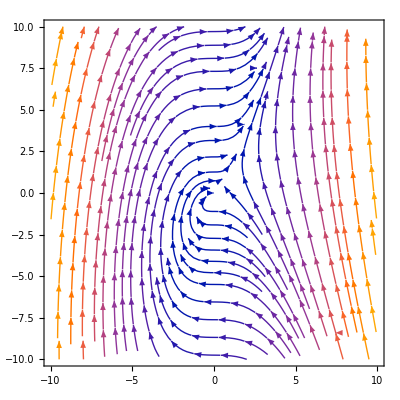

```mathematica
StreamPlot[{y-x, x^2}, {x, -10, 10}, {y, -10, 10}]
```

```mathematica
Clear["Global`*"]
 f[x_, y_] := y-x;
g[x_, y_] := x^2;
theta[x_, y_]:= ArcTan[g[x, y]/f[x, y]];
Index = (Integrate[D[theta[1, y], y],{y, -1, 1}] + 
Integrate[D[theta[x, -1],x],{x, -1, 1}] + Integrate[D[theta[-1, y], y],{y, 1, -1}]+
Integrate[D[theta[x, 1],x],{x, 1, -1}])/(2*π)
```

0

#### b)

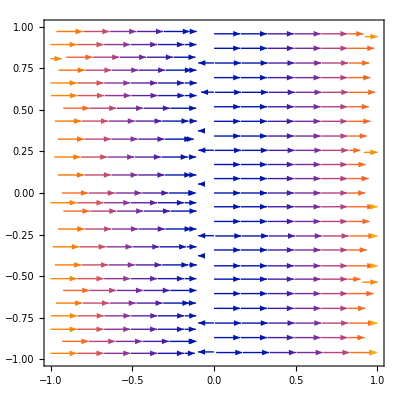

```mathematica
StreamPlot[{a * r + r^2, 0} /.{a->0.1},{r, -1, 1},{theta, -1, 1}]
```

```mathematica
Clear["Global`*"]
 f[a_, r_] := a * r + r^2;
g[a_, r_] := 0;
theta[x_, y_]:= ArcTan[g[x, y]/f[x, y]];
Index = (Integrate[D[theta[2, y], y],{y, -2, 2}] + 
Integrate[D[theta[x, -2],x],{x, -2, 2}] + Integrate[D[theta[-2, y], y],{y, 2, -2}]+
Integrate[D[theta[x, 2],x],{x, 2, -2}])/(2*π)
```

0

### c)

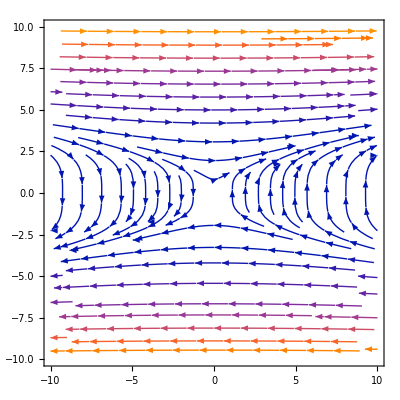

```mathematica
StreamPlot[{y^3, x}, {x, -10, 10}, {y, -10, 10}]
```

```mathematica
Clear["Global`*"]
 f[x_, y_] := y^3;
g[x_, y_] := x;
theta[x_, y_]:= ArcTan[g[x, y]/f[x, y]];
index = (Integrate[D[theta[2, y], y],{y, -2, 2}] + 
Integrate[D[theta[x, -2],x],{x, -2, 2}] + Integrate[D[theta[-2, y], y],{y, 2, -2}]+
Integrate[D[theta[x, 2],x],{x, 2, -2}])/(2*π);
N[index]
```

-1.

### d)

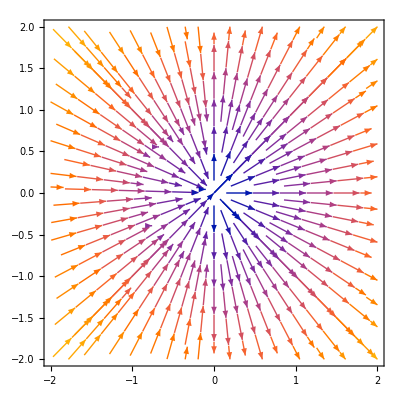

```mathematica
xDot = (x^2 + y^2)^(Abs[n]/2)*Cos[n * ArcTan[y/x]];
yDot = (x^2 + y^2)^(Abs[n/2]) * Sin[n*ArcTan[y/x]];
StreamPlot[{xDot, yDot} /.{n->1}, {x, -2, 2}, {y, -2, 2}]
```

```mathematica
Clear["Global`*"]
 f[x_, y_] :=(x^2 + y^2)^(Abs[n]/2)*Cos[n * ArcTan[y/x]];
g[x_, y_] := (x^2 + y^2)^(Abs[n/2]) * Sin[n*ArcTan[y/x]];
theta[x_, y_]:= ArcTan[g[x, y]/f[x, y]];
Index = (Integrate[D[theta[2, y], y],{y, -2, 2}] + 
Integrate[D[theta[x, -2],x],{x, -2, 2}] + Integrate[D[theta[-2, y], y],{y, 2, -2}]+
Integrate[D[theta[x, 2],x],{x, 2, -2}])/(2*π)
```

n